# Outer Products for Matrix Multiplication

## Technical Report, GSI Technology

Brian Beckman
Technology Fellow
November, 2023

## Abstract

Accumulated outer products are much faster than iterated inner products for matrix multiplication. Both are compared against Wolfram’s built-in. Neither beat the built-in, but that’s not the point. The point is that if you must code-up a matmul for whatever reason, say embedded hardware without libraries, you’re better off starting with accumulated outer product.

## Iterated Inner Product Versus Accumulated Outer Product

### Set Up

Set some array dimensions as mutually co-prime numbers, for generality.

Consider a small matrix of floating-point numbers in the range [0., 1.], inclusive both ends.

```mathematica
ClearAll[m,n,k,A,B];
m=5;k=4;n=7;GCD[m,k,n]
(A=RandomReal[{0.,1.},{m,k}])//MatrixForm
```

1

(0.382847 | 0.0694573 | 0.627889 | 0.646139
0.507911 | 0.465918 | 0.380455 | 0.698418
0.143523 | 0.400177 | 0.545172 | 0.221861
0.0517602 | 0.755199 | 0.539953 | 0.536782
0.533501 | 0.179299 | 0.849997 | 0.79486)

Natively, A is a List of rows with two levels of brackets. Indexing A yields a row vector, with only one level of brackets.

```mathematica
A[[2]]
```

{0.507911,0.465918,0.380455,0.698418}

To get a column of A, transpose a row of the transpose. Again, the result has only one level of brackets, so its type as a column vector is implicit. It has exactly the same shape as a row vector. This ambiguity is a defect. However, this defect is commonplace in programming languages.

```mathematica
Aᵀ[[2]]ᵀ
```

{0.0694573,0.465918,0.400177,0.755199,0.179299}

More helper functions

```mathematica
ClearAll[row,col];
row[M_,i_]:=M[[i]];
col[M_,i_]:=Mᵀ[[i]]ᵀ;
```

Make another matrix to play with.

```mathematica
(B=RandomReal[{0.,1.},{k,n}])//MatrixForm
```

(0.827434 | 0.343548 | 0.75827 | 0.433013 | 0.929009 | 0.969251 | 0.259242
0.0356246 | 0.867495 | 0.336331 | 0.693535 | 0.852175 | 0.872596 | 0.906007
0.0771809 | 0.926093 | 0.208394 | 0.413351 | 0.0669749 | 0.648475 | 0.115599
0.955218 | 0.643065 | 0.343872 | 0.182448 | 0.0591317 | 0.672056 | 0.242122)

Check Mathematica’s built-in matrix product.

```mathematica
(A.B)//MatrixForm
```

(0.984919 | 1.18877 | 0.666699 | 0.591374 | 0.495118 | 1.27309 | 0.391206
1.13337 | 1.38014 | 0.861288 | 0.827749 | 0.935678 | 1.61494 | 0.76688
0.387014 | 1.04401 | 0.433324 | 0.60551 | 0.523987 | 0.990936 | 0.516509
0.624149 | 1.51815 | 0.590352 | 0.867294 | 0.759551 | 1.42005 | 0.890018
1.27269 | 1.63715 | 0.915307 | 0.851731 | 0.752351 | 1.75895 | 0.591463)

### Iterated Inner Product

Iterate inner products -- a school algorithm -- row vectors times column vectors. The following shows row 2 of A inner-product col 2 of B to produce element (2,2) of the product A.B.

```mathematica
row[A,2].col[B,2]
```

1.38014

Here is iterated inner product compared for accuracy against the built-in, intrinsic matrix product.

```mathematica
On[Assert];
```

```mathematica
Assert[Module[{i,j,ab=ConstantArray[0.0,{m,n}]},
For[i=1,i<=m,i++,
For[j=1,j<=n,j++,
ab[[i,j]]=row[A,i].col[B,j]]];
ab]===A.B]
```

### Accumulated Outer Product

Check outer product:

```mathematica
Outer[Times,col[A,2],row[B,2]]//MatrixForm
```

(0.00247439 | 0.0602539 | 0.0233606 | 0.048171 | 0.0591897 | 0.0606082 | 0.0629288
0.0165981 | 0.404182 | 0.156703 | 0.323131 | 0.397044 | 0.406559 | 0.422125
0.0142561 | 0.347152 | 0.134592 | 0.277537 | 0.341021 | 0.349193 | 0.362564
0.0269036 | 0.655131 | 0.253997 | 0.523756 | 0.643561 | 0.658983 | 0.684215
0.00638743 | 0.155541 | 0.0603036 | 0.12435 | 0.152794 | 0.156455 | 0.162446)

Here is matrix product as accumulated outer product compared against the built-in, intrinsic matrix product. Notice there is only one loop, so this outer-product algorithm should be much faster than the iterated inner-product.

```mathematica
Assert[Module[{kk,ab=ConstantArray[0.0,{m,n}]},
For[kk=1,kk<=k,kk++,
ab+=Outer[Times,col[A,kk],row[B,kk]]];
ab]===A.B]
```

### Helper Functions

Even with these very small matrices, the accumulated outer product is much faster than the iterated inner product.

```mathematica
ClearAll[iteratedInnerProduct,accumulatedOuterProduct,builtInProduct];
iteratedInnerProduct[m_,k_,n_,A_,B_]:=
Module[{i,j,ab=ConstantArray[0.0,{m,n}],result,time},
{time,result}=AbsoluteTiming[
For[i=1,i<=m,i++,
For[j=1,j<=n,j++,
ab[[i,j]]=row[A,i].col[B,j]]];ab];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
accumulatedOuterProduct[m_,k_,n_,A_,B_]:=
Module[{kk,ab=ConstantArray[0.0,{m,n}],result,time},
{time,result}=AbsoluteTiming[
For[kk=1,kk<=k,kk++,
ab+=Outer[Times,col[A,kk],row[B,kk]]];ab];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
builtInProduct[m_,k_,n_,A_,B_]:=
Module[{kk,ab,result,time},
{time,result}=AbsoluteTiming[ab=A.B];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
With[{ab=builtInProduct[m,k,n,A,B],
abi=iteratedInnerProduct[m,k,n,A,B],
aba=accumulatedOuterProduct[m,k,n,A,B]},
Assert[ab["result"]===abi["result"]===aba["result"]];
Print[<|"built-in time"->ab["time"],
"inner time"->abi["time"],"outer time"->aba["time"],
"inner/outer ratio"->N[abi["time"]/aba["time"]],
"outer/built-in ratio"->N[aba["time"]/ab["time"]]|>];]
```

<|built-in time→3.×10^-6 s,inner time→0.000107 s,outer time→0.000017 s,inner/outer ratio→6.29412,outer/built-in ratio→5.66667|>

### Large Matrices

With the following dimensions, iterated inner product takes 20 minutes: too long to wait.

```mathematica
GCD[1001,1114,993]
```

1

Here are timings for square matrices of every 25 dims from 1 through 376:

```mathematica
ClearAll[timings];
(timings=With[{precision=1.*^-5},
Module[{timings=
Table[With[{m=d,k=d,n=d},
With[{A=RandomReal[{0.,1.},{m,k}],
B=RandomReal[{0.,1.},{k,n}]},
<|"dim"->d,
"built-in"->builtInProduct[m,k,n,A,B],
"inner"->iteratedInnerProduct[m,k,n,A,B],
"outer"->accumulatedOuterProduct[m,k,n,A,B]|>
]],{d,1,400,25}]},
Map[Assert[
Round[#["built-in"]["result"],precision]===
Round[#["inner"]["result"],precision]===
Round[#["outer"]["result"],precision]
]&,timings];
Map[{#["dim"],#["built-in"]["time"],#["inner"]["time"],#["outer"]["time"]}&,timings]
]])//MatrixForm
```

(1 | 2.×10^-6 s | 0.00001 s | 5.×10^-6 s
26 | 0.000021 s | 0.001819 s | 0.000096 s
51 | 0.000016 s | 0.008639 s | 0.000257 s
76 | 0.00026 s | 0.034524 s | 0.000707 s
101 | 0.001146 s | 0.065588 s | 0.00212 s
126 | 0.00008 s | 0.119771 s | 0.003335 s
151 | 0.000101 s | 0.178706 s | 0.004789 s
176 | 0.000335 s | 0.289882 s | 0.006121 s
201 | 0.000169 s | 0.460008 s | 0.00777 s
226 | 0.000206 s | 0.647442 s | 0.009434 s
251 | 0.000263 s | 0.938203 s | 0.011673 s
276 | 0.00034 s | 1.00636 s | 0.013534 s
301 | 0.00044 s | 1.40346 s | 0.019584 s
326 | 0.000861 s | 1.9191 s | 0.021801 s
351 | 0.000572 s | 2.43771 s | 0.026874 s
376 | 0.00086 s | 2.7252 s | 0.031177 s)

A log-linear plot of all the timings:

```mathematica
ClearAll[plottableTimings];
plottableTimings[j_]:={col[timings,1],(Log10@*QuantityMagnitude)[col[timings,j]]}ᵀ
```

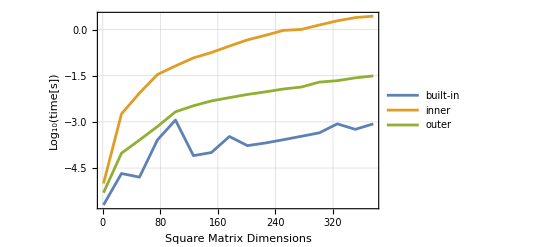

```mathematica
ListLinePlot[{plottableTimings[2],
plottableTimings[3],plottableTimings[4]},
(*ImageSize->Large,*)GridLines->Automatic,
Frame->True,PlotLegends->{"built-in","inner","outer"},
FrameLabel->{{"Log_10(time[s])",""},{"Square Matrix Dimensions","Running Times"}}]
```